# Directional flux analysis

#### Load trajectories

Load the {x,y} of all trajectories. Analysis of directional scaffold movement was performed only to scaffold-myosin complexes that moved for more than 6 continuous frames (3 sec) and covered a distance of more than 8 pixels (860 nm).

```mathematica
PlotTrajectories=Function[{filename,color},  
trajectory=Import[NotebookDirectory[]<>"sampleTrajectories.xls"];
(*Analysis of directional scaffold movement was performed only to scaffold-myosin complexes that moved for more than 6 continuous frames (3 sec) and covered a distance of more than 8 pixels (860 nm).*)

trajectoryFlag=Table[Boole[Length[trajectory⟦i⟧]≥6&&EuclideanDistance[trajectory⟦i,1⟧,trajectory⟦i,-1⟧]≥0.8/0.1071(*1 pixel = 0.1071 µm*)],{i,Length[trajectory]}];
trajectory=Pick[trajectory,trajectoryFlag,1];
cleanedTrajectory=trajectory;

ListLinePlot[cleanedTrajectory,Joined->True,PlotRange->{{1,512},{1,512}},AspectRatio->1,Frame->True,Axes->False,PlotStyle->color,ImageSize->512]];
```

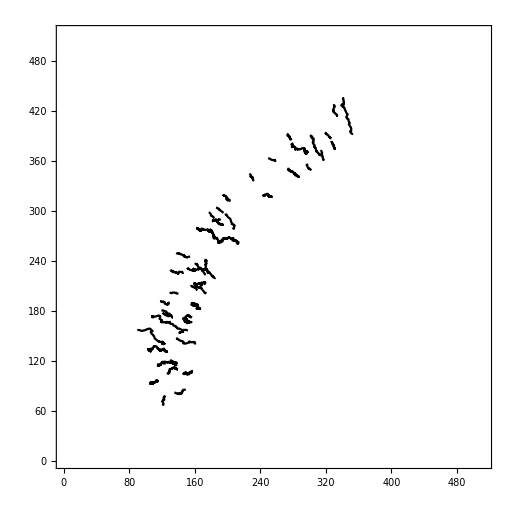

```mathematica
PlotTrajectories["sampleTrajectories",Black]
```

#### For each trajectory, compute the local actin polarity vector

```mathematica
Needs["Splines`"]
distance[{start_,end_},pt_]:=Module[{param},param=((pt-start).(end-start))/Norm[end-start]^2;(*parameter.the "." here means vector product*)Which[param<0,EuclideanDistance[start,pt],(*If outside bounds*)param>1,EuclideanDistance[end,pt],True,EuclideanDistance[pt,start+param (end-start)] (*Normal distance*)]];
```

```mathematica
(* Load the boundary of a keratocyte network *)
keratocyte={{415.6,371.5},{438.6,386.6},{406.6,379.5},{427.6,406.6},{396.6,390.6},{405.6,430.6},{377.5,400.6},{366.5,454.6},{357.5,390.6},{324.5,449.6},{344.5,377.5},{301.5,433.6},{316.5,360.5},{275.5,413.6},{286.5,337.5},{235.5,387.6},{260.5,320.5},{213.5,364.5},{236.5,290.5},{184.5,326.5},{216.5,264.5},{162.5,300.5},{201.5,240.5},{143.5,280.5},{190.5,212.5},{121.4,243.5},{171.5,176.5},{101.4,211.5},{165.5,150.5},{87.43,172.5},{166.5,133.5},{84.43,140.5},{171.5,120.4},{90.44,94.44},{176.5,120.4},{108.4,73.43},{185.5,105.4},{148.5,66.43}};
```

```mathematica
trajectory=cleanedTrajectory;
splineIndex={};
in={};
out={};
flagTrajectory={};
smoothTrajectory={};
Δ=0.05;
```

```mathematica
FitTrajectory=Function[{data},
dataOut=Table[data⟦2 i⟧,{i,Length[data]/2}];
dataIn=Table[data⟦2 i-1⟧,{i,Length[data]/2}];
sfOut=SplineFit[dataOut,Cubic];
sfIn=SplineFit[dataIn,Cubic]
];
FitTrajectory[keratocyte];
```

```mathematica
splineIndexCM={};
splineIndex={};
For[n=1,n≤Length[cleanedTrajectory],n++,

splineIndexTrajectory={};
inTrajectory={};
outTrajectory={};

data=trajectory⟦n⟧;

(* Find the center of mass of the trajectory *)
(* This coordinate will be used to calculate the local actin polarity vector *)

xCM=Mean[Table[trajectory⟦n,i,1⟧,{i,Length[trajectory⟦n⟧]}]];
yCM=Mean[Table[trajectory⟦n,i,2⟧,{i,Length[trajectory⟦n⟧]}]];
distList0=Table[distance[{sfOut[j],sfIn[j]},{xCM,yCM}],{j,1,sfIn⟦2,2⟧-1}];


index0=Table[j,{j,1,sfIn⟦2,2⟧-1}];
minIndex0=Flatten[Position[distList0,Min[distList0]]]⟦1⟧;
minParameter0=index0⟦minIndex0⟧;
distList1=Table[distance[{sfOut[j],sfIn[j]},{xCM,yCM}(*trajectory⟦n,i⟧*)],{j,minParameter0-1,minParameter0+1,Δ}];
index1=Table[j,{j,minParameter0-1,minParameter0+1,Δ}];
minIndex1=Flatten[Position[distList1,Min[distList1]]]⟦1⟧;

splineIndexTrajectory=Append[splineIndexTrajectory,index1⟦minIndex1⟧];
inTrajectory=Append[inTrajectory,sfIn[index1⟦minIndex1⟧]];
outTrajectory=Append[outTrajectory,sfOut[index1⟦minIndex1⟧]];

splineIndexCM=Append[splineIndexCM,index1⟦minIndex1⟧];

(* The movement direction for each trajectory was the calculated by comparing two Euclidian distances along the actin polarity field vector;(1) distance between starting point and cell periphery,∆xstart,and (2) distance between finish point and cell periphery,∆xfinish.Trajectories away from the cell center have a negative (∆xfinish–∆xstart),whereas trajectories toward the cell-center are positive. *)

distFirstOut=EuclideanDistance[data⟦1⟧,sfOut[splineIndexTrajectory⟦1⟧]];
distLastOut=EuclideanDistance[data⟦-1⟧,sfOut[splineIndexTrajectory⟦-1⟧]];

flag=0;
If[distFirstOut<distLastOut,flag=-1];
If[distFirstOut>distLastOut,flag=1];

flagTrajectory=Append[flagTrajectory,flag];
in=Append[in,inTrajectory];
out=Append[out,outTrajectory];
]
```

```mathematica
trajectoryOut=Pick[trajectory,flagTrajectory,1];
trajectoryIn=Pick[trajectory,flagTrajectory,-1];
```

### Plot to-cell-center and to-cell-periphery trajectories

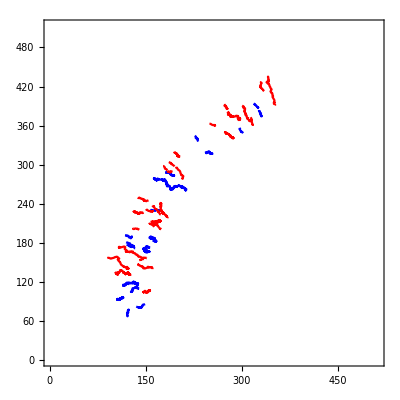

```mathematica
(* Plot the to-cell-center (blue) and to-cell-periphery (red) trajectories *)
Show[ListLinePlot[trajectoryOut,PlotStyle->Blue,AspectRatio->1,PlotRange->{{1,512},{1,512}},Axes->False,Frame->True],
ListLinePlot[trajectoryIn,PlotStyle->Red,AspectRatio->1,PlotRange->{{1,512},{1,512}},ImageSize->512,Axes->False,Frame->True]]
```